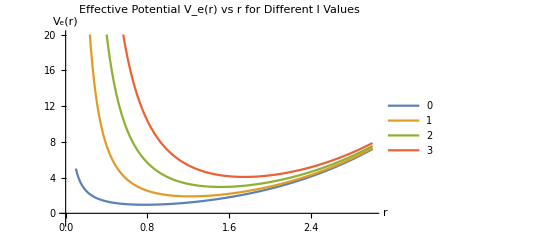

```mathematica
(*Define the potential function Ve(r)*)
V[r_,l_,ω_,λ_]:=1/2 ω^2 r^2+λ/32 r^4+1/(2 r)+(l(l+1))/(2 r^2)

(*Set range for r and parameters*)
rMin=0.1;
rMax=3.0;
λ=1;
ωr=1;
lValues={0,1,2,3};
(*Plot Ve(r) for different values of l*)
Plot[Evaluate[Table[Ve[r,l,ωr,λ],{l,lValues}]],{r,rMin,rMax},PlotRange->{-1,20},PlotLegends->Placed[LineLegend[ToString/@lValues,LabelStyle->{FontSize->12}],Right],AxesLabel->{"r",Subscript[V,e][r]},PlotStyle->Thick,PlotLabel->Style["Effective Potential V_e(r) vs r for Different l Values",14],GridLines->None]
```